```mathematica
IntegerPartitions[4]
```

{{4},{3,1},{2,2},{2,1,1},{1,1,1,1}}

```mathematica
JordanRank[sizes_]:=Module[{n,ranks},
n=Sum[i,{i, sizes}];
Sum[Join[Reverse[Range[i-1]], ConstantArray[0,n-i+1]], {i, sizes}]
]
```

```mathematica
JordanRanks[n_]:= Map[JordanRank, IntegerPartitions[n]]
```

```mathematica
JordanRanks[5]
```

{{4,3,2,1,0},{3,2,1,0,0},{3,1,0,0,0},{2,1,0,0,0},{2,0,0,0,0},{1,0,0,0,0},{0,0,0,0,0}}

```mathematica
PointwiseLE[JordanRank[{3,2}],JordanRank[{5}]]
```

True

```mathematica
FstLtSnd[lst_]:=lst[[1]]≤lst[[2]]
```

```mathematica
FstLtSnd[{1,5}]
```

True

```mathematica
PointwiseLE[a_,b_]:=AllTrue[Transpose@{a, b},FstLtSnd]
```

```mathematica
JordanRankOrder[a_, b_]:=PointwiseLE[JordanRank[b], JordanRank[a]]
```

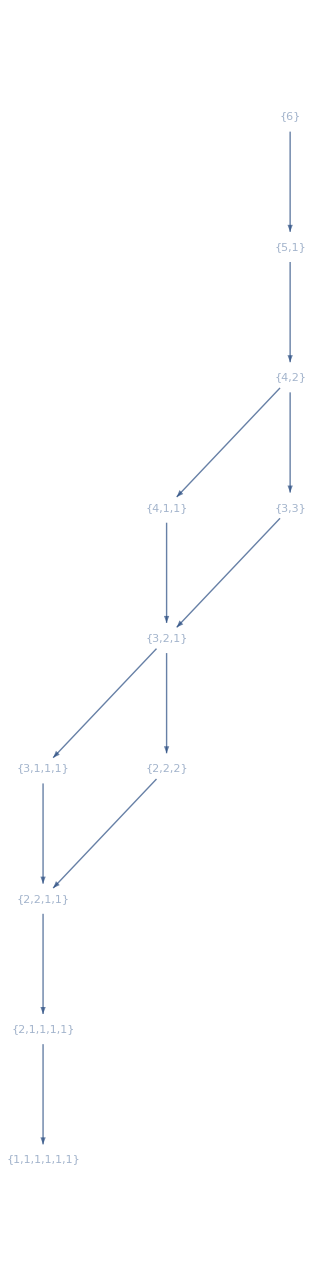

```mathematica
ResourceFunction["HasseDiagram"][JordanRankOrder, IntegerPartitions[6], VertexShapeFunction->"Name"]
```

```mathematica
Reverse[Range[0,2]]
```

{2,1,0}